```mathematica
SetDirectory[NotebookDirectory[]];
```

## Define Functions

```mathematica
BW[w_,wr_,Γ_,δbg_,const_,shift_,shift2_]:=
const((Γ/2)^2/((w-wr)^2+(Γ/2)^2))+ δbg((Γ/2)(w-wr))/((w-wr)^2+(Γ/2)^2)+0 ((4 (w-wr)^2- Γ^2) deltabg^2)/(4 (w-wr)^2+Γ^2)+shift (w-wr)+shift2 ;
BWi[w_,wr_,Γ_,const_]:=const((Γ/2)^2/((w-wr)^2+(Γ/2)^2)) ;

fit[input_,output_,Tscan_]:=Module[{temp=Range[1,Length[Tscan]],n,maxx,minx,maxy,maxyx,maxyi,maxxy,inter,maxxs,maxxis,maxys,mins,hwhmi,gammas,inputc,bad},
SetSharedVariable[temp];
ParallelDo[n=temp[[ii]];
maxx=Max[input[n][[All,1]]];
minx=Min[input[n][[All,1]]];
maxy=Max[input[n][[All,2]]];
maxyx=input[n][[Position[input[n],Max[input[n][[All,2]]]][[1,1]],1]];
maxyi=Position[input[n][[All,1]],maxyx][[1,1]];
maxxy=input[n][[Position[input[n],Max[input[n][[All,1]]]][[1,1]],2]];
inter=Interpolation[input[n],InterpolationOrder->1];maxxs=Sort[Quiet[DeleteDuplicatesBy[Table[{Round[FindMaxValue[{inter[x],minx+a≤x≤minx+2 a},{x,minx+a}],maxxy/30],FindArgMax[{inter[x],minx+a≤x≤minx+2 a},{x,minx+a}][[1]]},{a,0,1/2(maxx-minx),1/20}],First][[All,2]]]];
bad={};
If[Length[maxxs]>1,Do[If[maxxs[[i+1]]/maxxs[[i]]≤1.001,bad=Append[bad,{i}]],{i,Length[maxxs]-1}]];
maxxs=Delete[maxxs,bad];maxxis=Sort[Table[Position[input[n][[All,1]],Nearest[input[n][[All,1]],maxxs[[i]]][[1]]][[1,1]],{i,Length[maxxs]}]];
bad={};
Do[If[Or[input[n][[maxxis[[i]]-30,2]]>input[n][[maxxis[[i]],2]],input[n][[maxxis[[i]]+30,2]]>input[n][[maxxis[[i]],2]]],bad=Append[bad,{i}]],{i,Length[maxxis]}];maxxs=Delete[maxxs,bad];maxxis=Delete[maxxis,bad];
maxys=Table[input[n][[maxxis[[i]],2]],{i,Length[maxxs]}];
If[Length[maxxs]>1,
mins=Range[Length[maxxs]-1];
Do[mins[[i]]=Position[input[n][[All,2]],Min[input[n][[maxxis[[i]];;maxxis[[i+1]],2]]]][[1,1]],{i,Length[maxxs]-1}];mins=Append[Prepend[mins,maxxis[[1]]-(mins[[1]]-maxxis[[1]])],If[maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]])≤ Length[input[n]],maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]]),Length[input[n]]]];,
hwhmi=Position[input[n],Nearest[input[n][[;;maxyi,2]],maxy/2][[1]]][[1,1]];
mins={maxyi-3(maxyi-hwhmi),If[maxyi+3(maxyi-hwhmi)≤Length[input[n]],maxyi+3(maxyi-hwhmi),Length[input[n]]]};];
If[mins[[1]]≤0,mins[[1]]=1];
hwhmi=Range[Length[maxxs]];
Do[hwhmi[[i]]=Position[input[n],Nearest[input[n][[mins[[i]];;maxxis[[i]],2]],inter[maxxs[[i]]]/2][[1]]][[1,1]],{i,Length[maxxs]}];
gammas=Range[Length[hwhmi]];
Do[gammas[[i]]=2(maxxs[[i]]-input[n][[hwhmi[[i]],1]]),{i,Length[hwhmi]}];
inputc=Range[Length[maxxs]];
Do[inputc[[i]]=input[n][[If[i≥2,If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])<mins[[i]],mins[[i]],maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])],If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])>0,maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]]),1]];;If[maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]])<mins[[i+1]],maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]]),mins[[i+1]]]]],{i,Length[maxxs]}];
temp[[ii]]=Range[Length[hwhmi]];
Do[temp[[ii,i]]=NonlinearModelFit[inputc[[i]],{BW[w,wr,Γ,δbg,const,shift,shift2],const>0,Γ>0},{{wr,maxxs[[i]]},{Γ,gammas[[i]]},{const,maxys[[i]]},{δbg,0.0},{shift,0.0},{shift2,0.0}},w,MaxIterations->1000],{i,Length[hwhmi]}];,{ii,Length[Tscan]}];output=temp;];

store[param_,res_,model_]:=Module[{temp=ToString[res]},res=Range[Length[model]];
Do[res[[i]]=Range[Length[model[[i]]]],{i,Length[model]}];Do[Do[res[[i,ii]]=param/.model[[i,ii]]["BestFitParameters"],{ii,Length[res[[i]]]}],{i,Length[res]}];];

storearea[res_,model_]:=Module[{temp=ToString[res]},res=Range[Length[model]];
Do[res[[i]]=Range[Length[model[[i]]]],{i,Length[model]}];Do[Do[res[[i,ii]]=π/2(Γ/.model[[i,ii]]["BestFitParameters"])( const/.model[[i,ii]]["BestFitParameters"]),{ii,Length[res[[i]]]}],{i,Length[res]}];];
```

```mathematica
fitONE[input_]:=Module[{maxx,minx,maxy,maxyx,maxyi,maxxy,inter,maxxis,mins,hwhmi,bad},
maxx=Max[input[[All,1]]];
minx=Min[input[[All,1]]];
maxy=Max[input[[All,2]]];
maxyx=input[[Position[input,Max[input[[All,2]]]][[1,1]],1]];
maxyi=Position[input[[All,1]],maxyx][[1,1]];
maxxy=input[[Position[input,Max[input[[All,1]]]][[1,1]],2]];
inter=Interpolation[input,InterpolationOrder->1];maxxs=Sort[Quiet[DeleteDuplicatesBy[Table[{Round[FindMaxValue[{inter[x],minx+a≤x≤minx+2 a},{x,minx+a}],maxxy/30],FindArgMax[{inter[x],minx+a≤x≤minx+2 a},{x,minx+a}][[1]]},{a,1,1/2(maxx-minx),1/20}],First][[All,2]]]];bad={};
If[Length[maxxs]>1,Do[If[maxxs[[i+1]]/maxxs[[i]]≤1.001,bad=Append[bad,{i}]],{i,Length[maxxs]-1}]];
maxxs=Delete[maxxs,bad];maxxis=Sort[Table[Position[input[[All,1]],Nearest[input[[All,1]],maxxs[[i]]][[1]]][[1,1]],{i,Length[maxxs]}]];
bad={};
Do[If[Or[input[[maxxis[[i]]-30,2]]>input[[maxxis[[i]],2]],input[[maxxis[[i]]+30,2]]>input[[maxxis[[i]],2]]],bad=Append[bad,{i}]],{i,Length[maxxis]}];maxxs=Delete[maxxs,bad];maxxis=Delete[maxxis,bad];
maxys=Table[input[[maxxis[[i]],2]],{i,Length[maxxs]}];
If[Length[maxxs]>1,
mins=Range[Length[maxxs]-1];
Do[mins[[i]]=Position[input[[All,2]],Min[input[[maxxis[[i]];;maxxis[[i+1]],2]]]][[1,1]],{i,Length[maxxs]-1}];mins=Append[Prepend[mins,maxxis[[1]]-(mins[[1]]-maxxis[[1]])],If[maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]])≤ Length[input],maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]]),Length[input]]];,
hwhmi=Position[input,Nearest[input[[;;maxyi,2]],maxy/2][[1]]][[1,1]];
mins={maxyi-3(maxyi-hwhmi),If[maxyi+3(maxyi-hwhmi)≤Length[input],maxyi+3(maxyi-hwhmi),Length[input]]};];
If[mins[[1]]≤0,mins[[1]]=1];
hwhmi=Range[Length[maxxs]];
Do[hwhmi[[i]]=Position[input,Nearest[input[[mins[[i]];;maxxis[[i]],2]],inter[maxxs[[i]]]/2][[1]]][[1,1]],{i,Length[maxxs]}];
gammas=Range[Length[hwhmi]];
Do[gammas[[i]]=2(maxxs[[i]]-input[[hwhmi[[i]],1]]),{i,Length[hwhmi]}];
inputc=Range[Length[maxxs]];
Do[inputc[[i]]=input[[If[i≥2,If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])<mins[[i]],mins[[i]],maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])],If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])>0,maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]]),1]];;If[maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]])<mins[[i+1]],maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]]),mins[[i+1]]]]],{i,Length[maxxs]}];];
```

## Charmonium s-wave

### Import Data

```mathematica
Tscancorig={0.155};
```

```mathematica
Do[ccdata[n]=Import["spectra/swccT"<>ToString[Round[1000Tscancorig[[n]]]]<>"spectra.dat"];,{n,Length[Tscancorig]}];
```

```mathematica
Do[ccdatau[n]=Import["spectra/swccT"<>ToString[Round[1000Tscancorig[[n]]]]<>"uspectra.dat"];,{n,Length[Tscancorig]}];
```

```mathematica
Do[ccdatal[n]=Import["spectra/swccT"<>ToString[Round[1000Tscancorig[[n]]]]<>"lspectra.dat"];,{n,Length[Tscancorig]}];
```

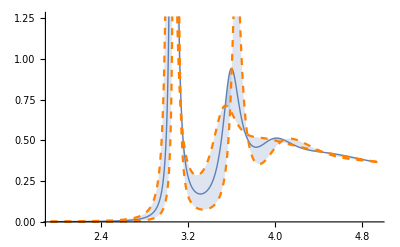

```mathematica
ListPlot[{ccdata[1],ccdatal[1],ccdatau[1]},Joined->True,Filling->{1->{2},1->{3}},PlotStyle->{Thick,{Dashed,Orange},{Dashed,Orange}}]
```

### Fitting

```mathematica
Clear[ccmodelu,ccmodell,ccmodel]
Quiet[fit[ccdata,ccmodel,Tscancorig]];
Quiet[fit[ccdatal,ccmodell,Tscancorig]];
Quiet[fit[ccdatau,ccmodelu,Tscancorig]];
```

```mathematica
Clear[wrfitcc,wrfitccl,wrfitccu,gfitcc,gfitccl,gfitccu,areafitcc,areafitccu,areafitccl,cfitcc,cfitccl,cfitccu,dfitcc,dfitccl,dfitccu,sfitcc,sfitccl,sfitccu,s2fitcc,s2fitccl,s2fitccu];
store[wr,wrfitcc,ccmodel];
store[wr,wrfitccl,ccmodell];
store[wr,wrfitccu,ccmodelu];
store[Γ,gfitcc,ccmodel];
store[Γ,gfitccl,ccmodell];
store[Γ,gfitccu,ccmodelu];
store[const,cfitcc,ccmodel];
store[const,cfitccl,ccmodell];
store[const,cfitccu,ccmodelu];
store[δbg,dfitcc,ccmodel];
store[δbg,dfitccl,ccmodell];
store[δbg,dfitccu,ccmodelu];
store[shift,sfitcc,ccmodel];
store[shift,sfitccl,ccmodell];
store[shift,sfitccu,ccmodelu];
store[shift2,s2fitcc,ccmodel];
store[shift2,s2fitccl,ccmodell];
store[shift2,s2fitccu,ccmodelu];
storearea[areafitcc,ccmodel];
storearea[areafitccl,ccmodell];
storearea[areafitccu,ccmodelu];
```

### Display Results

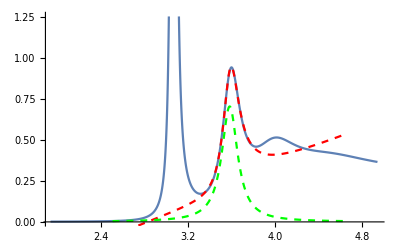

```mathematica
Block[{i=1,ii=2},Show[{ListPlot[ccdata[i],Joined->True],Plot[BW[x,wrfitcc[[i,ii]],gfitcc[[i,ii]],dfitcc[[i,ii]],cfitcc[[i,ii]],sfitcc[[i,ii]],s2fitcc[[i,ii]]],{x,0.7wrfitcc[[i,ii]],1.3wrfitcc[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitcc[[i,ii]],gfitcc[[i,ii]],cfitcc[[i,ii]]],{x,0.7wrfitcc[[i,ii]],1.3wrfitcc[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

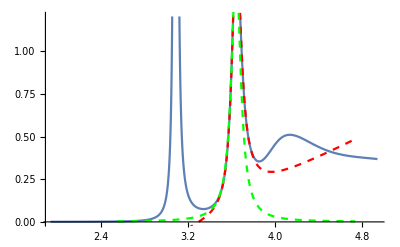

```mathematica
Block[{i=1,ii=2},Show[{ListPlot[ccdatal[i],Joined->True],Plot[BW[x,wrfitccl[[i,ii]],gfitccl[[i,ii]],dfitccl[[i,ii]],cfitccl[[i,ii]],sfitccl[[i,ii]],s2fitccl[[i,ii]]],{x,0.7wrfitccl[[i,ii]],1.3wrfitccl[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitccl[[i,ii]],gfitccl[[i,ii]],cfitccl[[i,ii]]],{x,0.7wrfitccl[[i,ii]],1.3wrfitccl[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

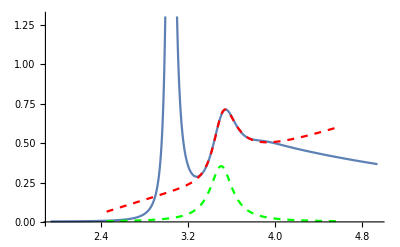

```mathematica
Block[{i=1,ii=2},Show[{ListPlot[ccdatau[i],Joined->True],Plot[BW[x,wrfitccu[[i,ii]],gfitccu[[i,ii]],dfitccu[[i,ii]],cfitccu[[i,ii]],sfitccu[[i,ii]],s2fitccu[[i,ii]]],{x,0.7wrfitccu[[i,ii]],1.3wrfitccu[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitccu[[i,ii]],gfitccu[[i,ii]],cfitccu[[i,ii]]],{x,0.7wrfitccu[[i,ii]],1.3wrfitccu[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

```mathematica
wrfitcc
```

{{3.06629,3.58192,3.93899}}

```mathematica
wrfitccu
```

{{3.03895,3.50444}}

```mathematica
wrfitccl
```

{{3.08595,3.64015}}

```mathematica
gfitcc
```

{{0.0350708,0.176772,0.333843}}

```mathematica
gfitccu
```

{{0.0573549,0.248}}

```mathematica
gfitccl
```

{{0.0156547,0.102724}}

#### Compare to AsReg

```mathematica
wrfitccAs={3.0658064062959536,3.5732752047264045,3.8764932660368197}
```

{3.06581,3.57328,3.87649}

```mathematica
wrfitccuAs={3.0375866017069706,3.4778758736274833,3.711954114124088}
```

{3.03759,3.47788,3.71195}

```mathematica
wrfitcclAs={3.0858576963586795,3.6348590610130156,3.929322792548011}
```

{3.08586,3.63486,3.92932}

```mathematica
gfitccAs={0.02770503001654519,0.11911344091387684,0.2882353898465183}
```

{0.027705,0.119113,0.288235}

```mathematica
gfitccuAs={0.04365882579753467,0.15469051483195329,0.20882606588811828}
```

{0.0436588,0.154691,0.208826}

```mathematica
gfitcclAs={0.012981582977874731,0.07472950327873716,0.498670833400382}
```

{0.0129816,0.0747295,0.498671}

## Charmonium p-wave

### Import Data

```mathematica
Tscancorig={0.155};
```

```mathematica
Do[ccdatap[n]=Import["spectra/pwccT"<>ToString[Round[1000Tscancorig[[n]]]]<>"spectra.dat"]/.{a_,b_}:>{a,-b};,{n,Length[Tscancorig]}];
Do[ccdatapu[n]=Import["spectra/pwccT"<>ToString[Round[1000Tscancorig[[n]]]]<>"uspectra.dat"]/.{a_,b_}:>{a,-b};,{n,Length[Tscancorig]}];
Do[ccdatapl[n]=Import["spectra/pwccT"<>ToString[Round[1000Tscancorig[[n]]]]<>"lspectra.dat"]/.{a_,b_}:>{a,-b};,{n,Length[Tscancorig]}];
```

```mathematica
Do[ccdatapAS[n]=Import["../../spectraldata/Tscan/Asreg/cc/pwccT"<>ToString[Round[1000Tscancorig[[n]]]]<>"spectra.dat"]/.{a_,b_}:>{a,b};,{n,Length[Tscancorig]}];
Do[ccdatapuAS[n]=Import["../../spectraldata/Tscan/Asreg/cc/pwccT"<>ToString[Round[1000Tscancorig[[n]]]]<>"uspectra.dat"]/.{a_,b_}:>{a,b};,{n,Length[Tscancorig]}];
Do[ccdataplAS[n]=Import["../../spectraldata/Tscan/Asreg/cc/pwccT"<>ToString[Round[1000Tscancorig[[n]]]]<>"lspectra.dat"]/.{a_,b_}:>{a,b};,{n,Length[Tscancorig]}];
```

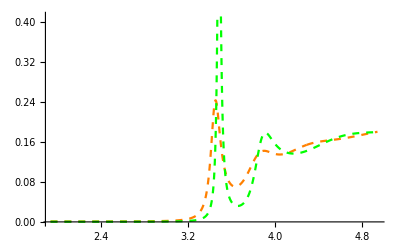

```mathematica
ListPlot[{ccdatap[1],ccdataplAS[1]},Joined->True,PlotStyle->{{Dashed,Orange},{Dashed,Green}}]
```

### Fitting

```mathematica
Clear[ccmodelpu,ccmodelpl,ccmodelp]
Quiet[fit[ccdatap,ccmodelp,Tscancorig]];
Quiet[fit[ccdatapl,ccmodelpl,Tscancorig]];
Quiet[fit[ccdatapu,ccmodelpu,Tscancorig]];
```

```mathematica
Clear[wrfitccp,wrfitccpl,wrfitccpu,gfitccp,gfitccpl,gfitccpu,areafitccp,areafitccpu,areafitccpl,cfitccp,cfitccpl,cfitccpu,dfitccp,dfitccpl,dfitccpu,sfitccp,sfitccpl,sfitccpu,s2fitccp,s2fitccpl,s2fitccpu];
store[wr,wrfitccp,ccmodelp];
store[wr,wrfitccpl,ccmodelpl];
store[wr,wrfitccpu,ccmodelpu];
store[Γ,gfitccp,ccmodelp];
store[Γ,gfitccpl,ccmodelpl];
store[Γ,gfitccpu,ccmodelpu];
store[const,cfitccp,ccmodelp];
store[const,cfitccpl,ccmodelpl];
store[const,cfitccpu,ccmodelpu];
store[δbg,dfitccp,ccmodelp];
store[δbg,dfitccpl,ccmodelpl];
store[δbg,dfitccpu,ccmodelpu];
store[shift,sfitccp,ccmodelp];
store[shift,sfitccpl,ccmodelpl];
store[shift,sfitccpu,ccmodelpu];
store[shift2,s2fitccp,ccmodelp];
store[shift2,s2fitccpl,ccmodelpl];
store[shift2,s2fitccpu,ccmodelpu];
storearea[areafitccp,ccmodelp];
storearea[areafitccpl,ccmodelpl];
storearea[areafitccpu,ccmodelpu];
```

### Display Results

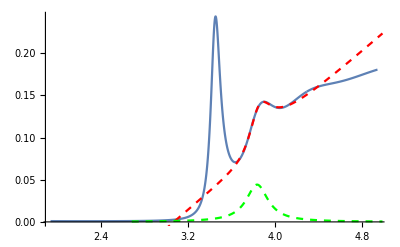

```mathematica
Block[{i=1,ii=2},Show[{ListPlot[ccdatap[i],Joined->True],Plot[BW[x,wrfitccp[[i,ii]],gfitccp[[i,ii]],dfitccp[[i,ii]],cfitccp[[i,ii]],sfitccp[[i,ii]],s2fitccp[[i,ii]]],{x,0.7wrfitccp[[i,ii]],1.3wrfitccp[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitccp[[i,ii]],gfitccp[[i,ii]],cfitccp[[i,ii]]],{x,0.7wrfitccp[[i,ii]],1.3wrfitccp[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

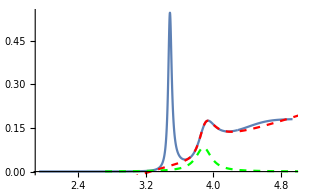

```mathematica
Block[{i=1,ii=2},Show[{ListPlot[ccdatapl[i],Joined->True],Plot[BW[x,wrfitccpl[[i,ii]],gfitccpl[[i,ii]],dfitccpl[[i,ii]],cfitccpl[[i,ii]],sfitccpl[[i,ii]],s2fitccpl[[i,ii]]],{x,0.7wrfitccpl[[i,ii]],1.3wrfitccpl[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitccpl[[i,ii]],gfitccpl[[i,ii]],cfitccpl[[i,ii]]],{x,0.7wrfitccpl[[i,ii]],1.3wrfitccpl[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

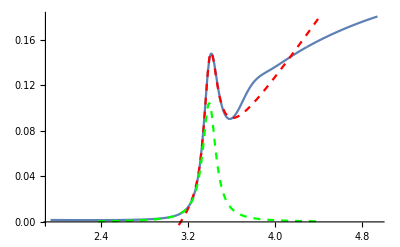

```mathematica
Block[{i=1,ii=1},Show[{ListPlot[ccdatapu[i],Joined->True],Plot[BW[x,wrfitccpu[[i,ii]],gfitccpu[[i,ii]],dfitccpu[[i,ii]],cfitccpu[[i,ii]],sfitccpu[[i,ii]],s2fitccpu[[i,ii]]],{x,0.7wrfitccpu[[i,ii]],1.3wrfitccpu[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitccpu[[i,ii]],gfitccpu[[i,ii]],cfitccpu[[i,ii]]],{x,0.7wrfitccpu[[i,ii]],1.3wrfitccpu[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

```mathematica
wrfitccp
```

{{3.4454,3.83373}}

```mathematica
wrfitccpu
```

{{3.39391}}

```mathematica
wrfitccpl
```

{{3.48497,3.88443}}

```mathematica
gfitccp
```

{{0.10406,0.243598}}

```mathematica
gfitccpu
```

{{0.14634}}

```mathematica
gfitccpl
```

{{0.050531,0.222544}}

#### Compare to AsReg

```mathematica
wrfitccpAs={3.4407424765136634,3.786408870677617}
```

{3.44074,3.78641}

```mathematica
wrfitccpuAs={3.381131907789358,3.640928021152156}
```

{3.38113,3.64093}

```mathematica
wrfitccplAs={3.483833742093671,3.855809505621743}
```

{3.48383,3.85581}

```mathematica
gfitccpAs={0.07398850415507063,0.19406572853809875}
```

{0.0739885,0.194066}

```mathematica
gfitccpuAs={0.10621815286347733,0.19633483511775973}
```

{0.106218,0.196335}

```mathematica
gfitcclpAs={0.03814624830767023,0.20617474630404634}
```

{0.0381462,0.206175}

## Bottomonium s-wave

### Import Data

```mathematica
Tscancorig={0.155};
```

```mathematica
Do[bbdata[n]=Import["spectra/swbbT"<>ToString[Round[1000Tscancorig[[n]]]]<>"spectra.dat"];,{n,Length[Tscancorig]}];
```

```mathematica
Do[bbdatau[n]=Import["spectra/swbbT"<>ToString[Round[1000Tscancorig[[n]]]]<>"uspectra.dat"];,{n,Length[Tscancorig]}];
```

```mathematica
Do[bbdatal[n]=Import["spectra/swbbT"<>ToString[Round[1000Tscancorig[[n]]]]<>"lspectra.dat"];,{n,Length[Tscancorig]}];
```

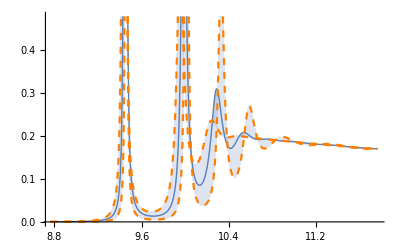

```mathematica
ListPlot[{bbdata[1],bbdatal[1],bbdatau[1]},Joined->True,Filling->{1->{2},1->{3}},PlotStyle->{Thick,{Dashed,Orange},{Dashed,Orange}}]
```

### Fitting

```mathematica
Clear[bbmodelu,bbmodell,bbmodel]
Quiet[fit[bbdata,bbmodel,Tscancorig]];
Quiet[fit[bbdatal,bbmodell,Tscancorig]];
Quiet[fit[bbdatau,bbmodelu,Tscancorig]];
```

```mathematica
Clear[wrfitbb,wrfitbbl,wrfitbbu,gfitbb,gfitbbl,gfitbbu,areafitbb,areafitbbu,areafitbbl,cfitbb,cfitbbl,cfitbbu,dfitbb,dfitbbl,dfitbbu,sfitbb,sfitbbl,sfitbbu,s2fitbb,s2fitbbl,s2fitbbu];
store[wr,wrfitbb,bbmodel];
store[wr,wrfitbbl,bbmodell];
store[wr,wrfitbbu,bbmodelu];
store[Γ,gfitbb,bbmodel];
store[Γ,gfitbbl,bbmodell];
store[Γ,gfitbbu,bbmodelu];
store[const,cfitbb,bbmodel];
store[const,cfitbbl,bbmodell];
store[const,cfitbbu,bbmodelu];
store[δbg,dfitbb,bbmodel];
store[δbg,dfitbbl,bbmodell];
store[δbg,dfitbbu,bbmodelu];
store[shift,sfitbb,bbmodel];
store[shift,sfitbbl,bbmodell];
store[shift,sfitbbu,bbmodelu];
store[shift2,s2fitbb,bbmodel];
store[shift2,s2fitbbl,bbmodell];
store[shift2,s2fitbbu,bbmodelu];
storearea[areafitbb,bbmodel];
storearea[areafitbbl,bbmodell];
storearea[areafitbbu,bbmodelu];
```

### Display Results

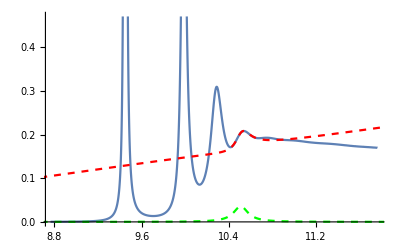

```mathematica
Block[{i=1,ii=4},Show[{ListPlot[bbdata[i],Joined->True],Plot[BW[x,wrfitbb[[i,ii]],gfitbb[[i,ii]],dfitbb[[i,ii]],cfitbb[[i,ii]],sfitbb[[i,ii]],s2fitbb[[i,ii]]],{x,0.7wrfitbb[[i,ii]],1.3wrfitbb[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitbb[[i,ii]],gfitbb[[i,ii]],cfitbb[[i,ii]]],{x,0.7wrfitbb[[i,ii]],1.3wrfitbb[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

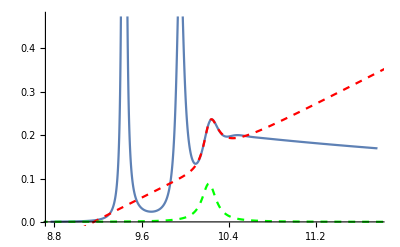

```mathematica
Block[{i=1,ii=3},Show[{ListPlot[bbdatau[i],Joined->True],Plot[BW[x,wrfitbbu[[i,ii]],gfitbbu[[i,ii]],dfitbbu[[i,ii]],cfitbbu[[i,ii]],sfitbbu[[i,ii]],s2fitbbu[[i,ii]]],{x,0.7wrfitbbu[[i,ii]],1.3wrfitbbu[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitbbu[[i,ii]],gfitbbu[[i,ii]],cfitbbu[[i,ii]]],{x,0.7wrfitbbu[[i,ii]],1.3wrfitbbu[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

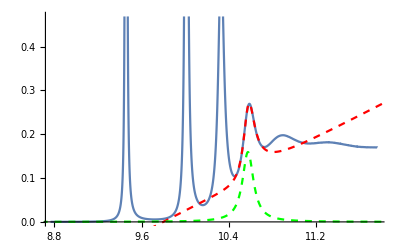

```mathematica
Block[{i=1,ii=4},Show[{ListPlot[bbdatal[i],Joined->True],Plot[BW[x,wrfitbbl[[i,ii]],gfitbbl[[i,ii]],dfitbbl[[i,ii]],cfitbbl[[i,ii]],sfitbbl[[i,ii]],s2fitbbl[[i,ii]]],{x,0.7wrfitbbl[[i,ii]],1.3wrfitbbl[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitbbl[[i,ii]],gfitbbl[[i,ii]],cfitbbl[[i,ii]]],{x,0.7wrfitbbl[[i,ii]],1.3wrfitbbl[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

```mathematica
wrfitbb
```

{{9.44917,9.98438,10.2778,10.5085}}

```mathematica
wrfitbbu
```

{{9.43804,9.95013,10.2168}}

```mathematica
wrfitbbl
```

{{9.45676,10.0093,10.327,10.5748}}

```mathematica
gfitbb
```

{{0.00740201,0.0476776,0.11635,0.162805}}

```mathematica
gfitbbu
```

{{0.0126996,0.0781462,0.156508}}

```mathematica
gfitbbl
```

{{0.00308532,0.0213672,0.0615252,0.122829}}

#### Compare to AsReg

```mathematica
wrfitbbAs={9.449160725537846,9.983721810494815,10.274338982921428,10.487992201361239}
```

{9.44916,9.98372,10.2743,10.488}

```mathematica
wrfitbbuAs={9.438007500314368,9.94829169393643,10.202099793075238,10.376807798794077}
```

{9.43801,9.94829,10.2021,10.3768}

```mathematica
wrfitbblAs={9.45675753400915,10.009172180532858,10.325830160934537,10.566092542682753}
```

{9.45676,10.0092,10.3258,10.5661}

```mathematica
gfitbbAs={0.006851363370286378,0.03731247454355584,0.08282182344586195,0.12147723591529277}
```

{0.00685136,0.0373125,0.0828218,0.121477}

```mathematica
gfitbbuAs={0.011626845394292032,0.05791139162573072,0.11047716498909083,0.12477545787569262}
```

{0.0116268,0.0579114,0.110477,0.124775}

```mathematica
gfitbblpAs={0.0028951027331795684,0.017635191917600716,0.04586916489230002,0.09483783836363115}
```

{0.0028951,0.0176352,0.0458692,0.0948378}

## Bottomonium p-wave

### Import Data

```mathematica
Tscancorig={0.155};
```

```mathematica
Do[bbdatap[n]=Import["spectra/pwbbT"<>ToString[Round[1000Tscancorig[[n]]]]<>"spectra.dat"]/.{a_,b_}:>{a,-b};,{n,Length[Tscancorig]}];
Do[bbdatapu[n]=Import["spectra/pwbbT"<>ToString[Round[1000Tscancorig[[n]]]]<>"uspectra.dat"]/.{a_,b_}:>{a,-b};,{n,Length[Tscancorig]}];
Do[bbdatapl[n]=Import["spectra/pwbbT"<>ToString[Round[1000Tscancorig[[n]]]]<>"lspectra.dat"]/.{a_,b_}:>{a,-b};,{n,Length[Tscancorig]}];
```

```mathematica
Do[bbdatapAS[n]=Import["../../spectraldata/Tscan/Asreg/bb/pwbbT"<>ToString[Round[1000Tscancorig[[n]]]]<>"spectra.dat"]/.{a_,b_}:>{a,b};,{n,Length[Tscancorig]}];
Do[bbdatapuAS[n]=Import["../../spectraldata/Tscan/Asreg/bb/pwbbT"<>ToString[Round[1000Tscancorig[[n]]]]<>"uspectra.dat"]/.{a_,b_}:>{a,b};,{n,Length[Tscancorig]}];
Do[bbdataplAS[n]=Import["../../spectraldata/Tscan/Asreg/bb/pwbbT"<>ToString[Round[1000Tscancorig[[n]]]]<>"lspectra.dat"]/.{a_,b_}:>{a,b};,{n,Length[Tscancorig]}];
```

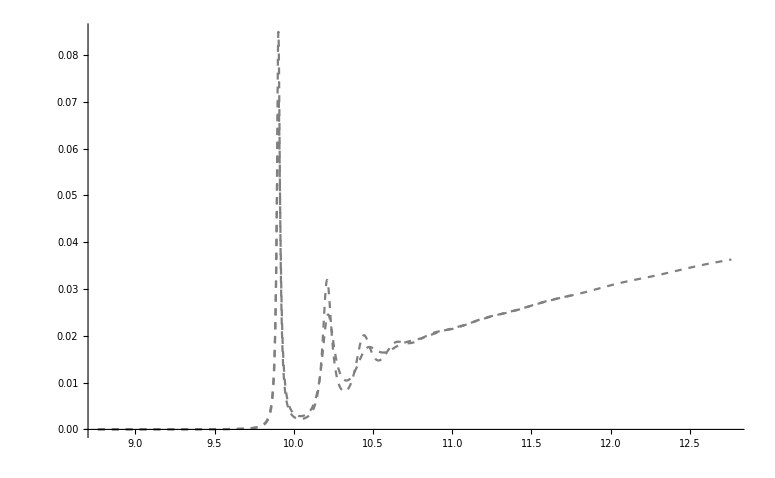

```mathematica
ListPlot[{bbdatap[1],bbdatapAS[1]},Joined->True,PlotStyle->{{Dashed,Gray},{Dashed,Gray}}]
```

### Fitting

```mathematica
Clear[bbmodelpu,bbmodelpl,bbmodelp]
Quiet[fit[bbdatap,bbmodelp,Tscancorig]];
Quiet[fit[bbdatapl,bbmodelpl,Tscancorig]];
Quiet[fit[bbdatapu,bbmodelpu,Tscancorig]];
```

```mathematica
Clear[wrfitbbp,wrfitbbpl,wrfitbbpu,gfitbbp,gfitbbpl,gfitbbpu,areafitbbp,areafitbbpl,areafitbbpu,cfitbbp,cfitbbpl,cfitbbpu,dfitbbp,dfitbbpl,dfitbbpu,sfitbbp,sfitbbpl,sfitbbpu,s2fitbbp,s2fitbbpl,s2fitbbpu];
store[wr,wrfitbbp,bbmodelp];
store[wr,wrfitbbpl,bbmodelpl];
store[wr,wrfitbbpu,bbmodelpu];
store[Γ,gfitbbp,bbmodelp];
store[Γ,gfitbbpl,bbmodelpl];
store[Γ,gfitbbpu,bbmodelpu];
store[const,cfitbbp,bbmodelp];
store[const,cfitbbpl,bbmodelpl];
store[const,cfitbbpu,bbmodelpu];
store[δbg,dfitbbp,bbmodelp];
store[δbg,dfitbbpl,bbmodelpl];
store[δbg,dfitbbpu,bbmodelpu];
store[shift,sfitbbp,bbmodelp];
store[shift,sfitbbpl,bbmodelpl];
store[shift,sfitbbpu,bbmodelpu];
store[shift2,s2fitbbp,bbmodelp];
store[shift2,s2fitbbpl,bbmodelpl];
store[shift2,s2fitbbpu,bbmodelpu];
storearea[areafitbbp,bbmodelp];
storearea[areafitbbpl,bbmodelpl];
storearea[areafitbbpu,bbmodelpu];
```

### Display Results

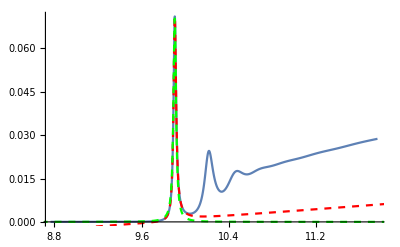

```mathematica
Block[{i=1,ii=1},Show[{ListPlot[bbdatap[i],Joined->True],Plot[BW[x,wrfitbbp[[i,ii]],gfitbbp[[i,ii]],dfitbbp[[i,ii]],cfitbbp[[i,ii]],sfitbbp[[i,ii]],s2fitbbp[[i,ii]]],{x,0.7wrfitbbp[[i,ii]],1.3wrfitbbp[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitbbp[[i,ii]],gfitbbp[[i,ii]],cfitbbp[[i,ii]]],{x,0.7wrfitbbp[[i,ii]],1.3wrfitbbp[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

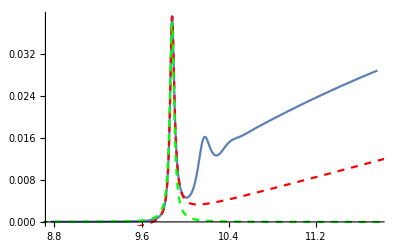

```mathematica
Block[{i=1,ii=1},Show[{ListPlot[bbdatapu[i],Joined->True],Plot[BW[x,wrfitbbpu[[i,ii]],gfitbbpu[[i,ii]],dfitbbpu[[i,ii]],cfitbbpu[[i,ii]],sfitbbpu[[i,ii]],s2fitbbpu[[i,ii]]],{x,0.7wrfitbbpu[[i,ii]],1.3wrfitbbpu[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitbbpu[[i,ii]],gfitbbpu[[i,ii]],cfitbbpu[[i,ii]]],{x,0.7wrfitbbpu[[i,ii]],1.3wrfitbbpu[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

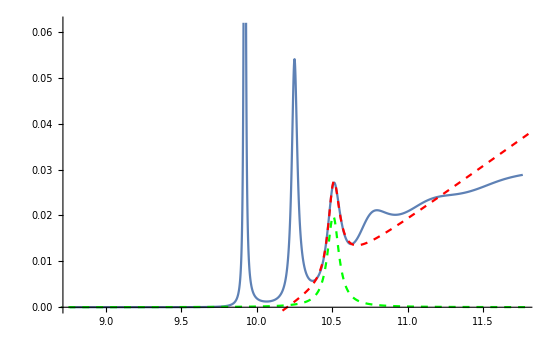

```mathematica
Block[{i=1,ii=3},Show[{ListPlot[bbdatapl[i],Joined->True],Plot[BW[x,wrfitbbpl[[i,ii]],gfitbbpl[[i,ii]],dfitbbpl[[i,ii]],cfitbbpl[[i,ii]],sfitbbpl[[i,ii]],s2fitbbpl[[i,ii]]],{x,0.7wrfitbbpl[[i,ii]],1.3wrfitbbpl[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitbbpl[[i,ii]],gfitbbpl[[i,ii]],cfitbbpl[[i,ii]]],{x,0.7wrfitbbpl[[i,ii]],1.3wrfitbbpl[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

```mathematica
wrfitbbp
```

{{9.90314,10.2108,10.4521}}

```mathematica
wrfitbbpu
```

{{9.87762,10.1622}}

```mathematica
wrfitbbpl
```

{{9.92121,10.2498,10.507}}

```mathematica
gfitbbp
```

{{0.0287599,0.0901991,0.13782}}

```mathematica
gfitbbpu
```

{{0.0479693,0.116871}}

```mathematica
gfitbbpl
```

{{0.0124981,0.0444984,0.0911278}}

#### Compare to AsReg

```mathematica
wrfitbbpAs={9.902882936350942,10.208480730715225,10.42894526516954,10.62621933479368}
```

{9.90288,10.2085,10.4289,10.6262}

```mathematica
wrfitbbpuAs={9.87682658643544,10.148786355803901,10.340395996413964}
```

{9.87683,10.1488,10.3404}

```mathematica
wrfitbbplAs={9.921171700139002,10.249140432498306,10.501751123159739,10.71164285197387}
```

{9.92117,10.2491,10.5018,10.7116}

```mathematica
gfitbbpAs={0.02392179985341772,0.06639523162743974,0.10972493549939222,0.13468325534244827}
```

{0.0239218,0.0663952,0.109725,0.134683}

```mathematica
gfitbbpuAs={0.038710387731434696,0.09379291076381072,0.11395224269674994}
```

{0.0387104,0.0937929,0.113952}

```mathematica
gfitbblpAs={0.010805321847905884,0.03410110666495143,0.0711169818336302,0.20173266966154974}
```

{0.0108053,0.0341011,0.071117,0.201733}